Solve for the EPs

```mathematica
y = -x^3+a x+b
S=Solve[-x^3+d x+c==0,x]//FullSimplify
```

b+a x-x^3

{{x→-(2 3^(1/3) d+2^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3))/(6^(2/3) (-9 c+√(81 c^2-12 d^3))^(1/3))},{x→((-1)^(1/3) (2 3^(1/3) d-(-2)^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3)))/(6^(2/3) (-9 c+√(81 c^2-12 d^3))^(1/3))},{x→(-2 (-3)^(2/3) d+(-6)^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3))/(3 2^(2/3) (-9 c+√(81 c^2-12 d^3))^(1/3))}}

```mathematica
Manipulate[Plot[y/.{a->alpha,b->beta},{x,-5,5}],{{alpha,2,"Curvature"},-10,10},{{beta,0,"Selection"},-10,10}]
```

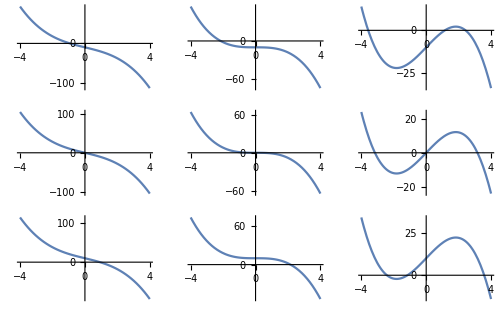

```mathematica
;
GraphicsGrid[plots,ImageSize->500]
```

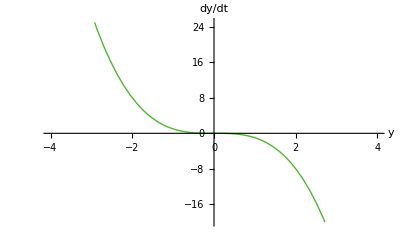
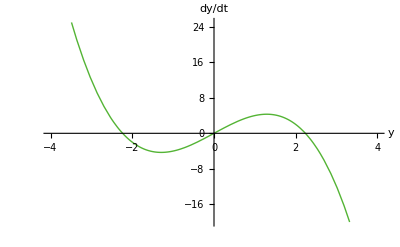
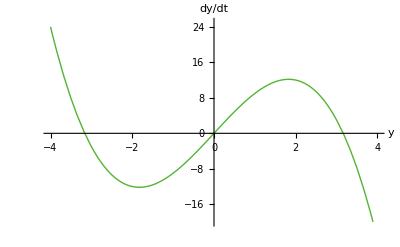
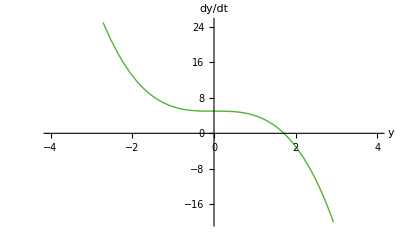
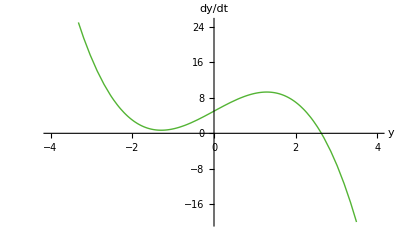
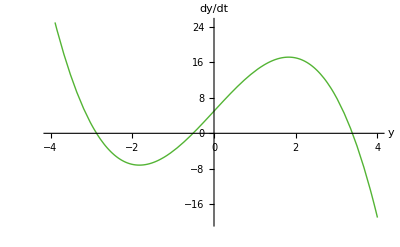
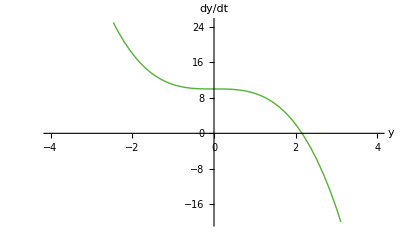
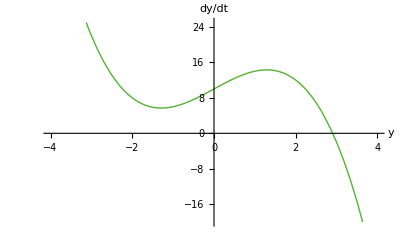

cubic.png

```mathematica
plots=Table[Plot[y=-x^3+a x+b,{x,-4,4},PlotStyle->{Thick,RGBColor[84/255,180/255,53/255]},PlotRange->{-20,25},AxesLabel->{"y","dy/dt"}],{b,{0,5,10}},{a,{0,5,10}}]
imgs=Transpose@plots;
g=Graphics[MapIndexed[Inset[#,#2]&,imgs,{2}],PlotRange->Thread[{1/4,2/3+Dimensions@imgs}],Axes->True,Ticks->{{{1,"0"},{2,"5"},{3,"10"}},{{1-0.05,"0"},{2-0.05,"5"},{3-0.05,"10"}}},AxesStyle->{{Thick,Arrowheads[0.03]},{Thick,Arrowheads[0.03]}},AxesOrigin->{1/4,1/4},ImageSize->700];
Export["cubic.png",Labeled[%,{"β_1","β_2"},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[Gray, Medium,FontFamily->"Helvetica",FontSize->25]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["cubic.png"]]]
```

```mathematica
SystemOpen["cubic.png"]
```

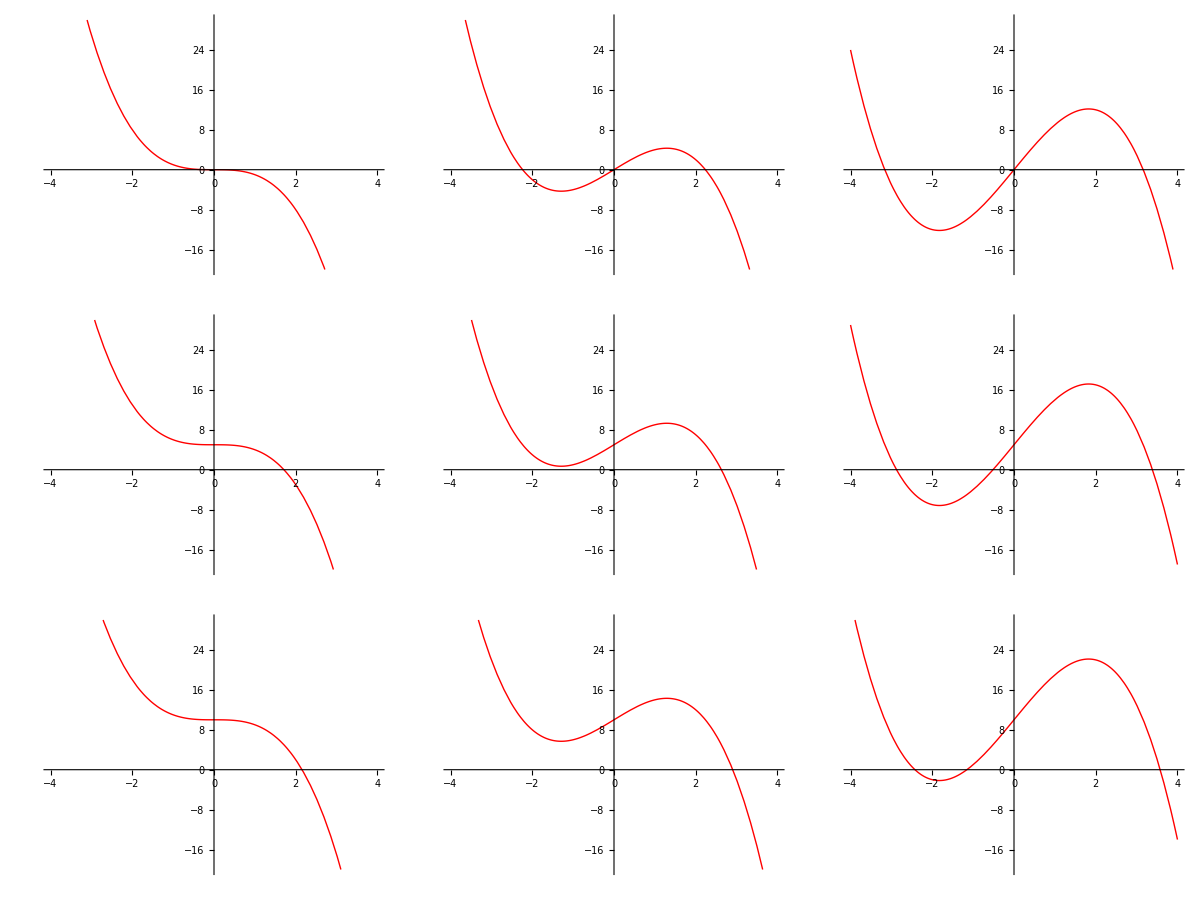

```mathematica
Grid[plots,Dividers->All,Spacings->1.5 {1,1}]
```

```mathematica
ReplacePart[%58,1->Prepend[First[%58],{"β_2=0","",""}]]
```

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[58,{β_2=0,,}].

Out::intm: Machine-sized integer expected at position 1 in Out[Prepend[58,{β_2=0,,}]].

Out[Prepend[58,{β_2=0,,}]]

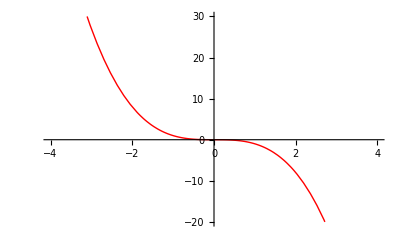
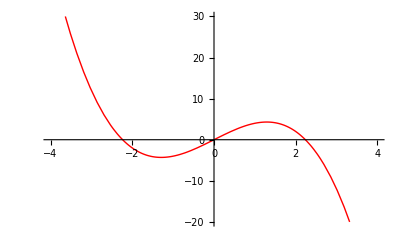
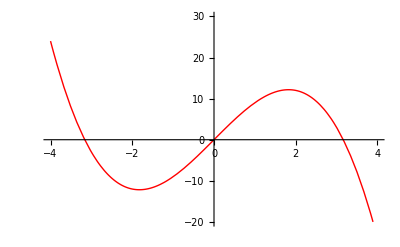
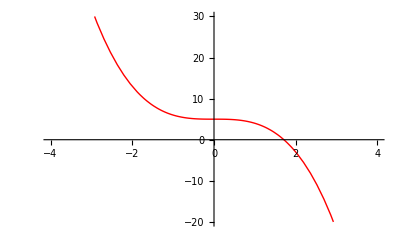
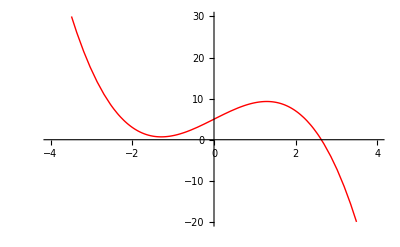
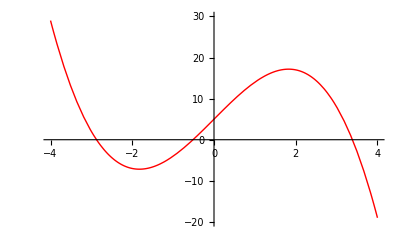
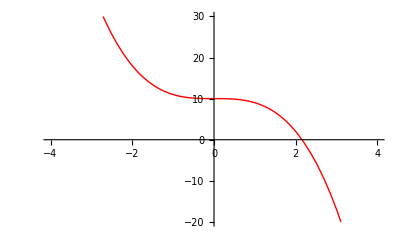
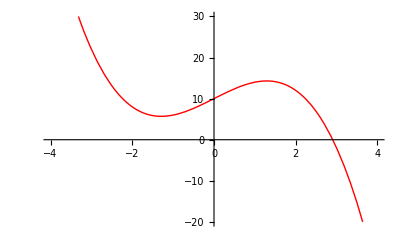
```mathematica
{{Subscript[β, 2]=0, Subscript[β, 2]=5, Subscript[β, 2]=10}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}}
```

0 | 5 | 10
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}[1][1]

```mathematica
Dimensions[%63]
```

{3,3}

```mathematica
ReplacePart[%46,1->Prepend[First[%46],{"ads","",""}]]
```

```mathematica
Dimensions[%42]
```

{3,3}